```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
Get["../../lib/lib2.m"];
Get["../../lib/util.m"];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools,newtxtext,newtxmath}"}, FontSize->12];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
texStyle={FontFamily->"Times",FontSize->12};
```

```mathematica
cm = 72/2.54;
```

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
```

```mathematica
plotsDir = "../../../plots/plots-thesis";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
files = FileNames[All, "../../../runs/Trials/N9K9/pert"];
data = Monitor[Table[Import[files[[k]]], {k, 1, 2}], ProgressIndicator[(k-1)/(Length[files]-1)]];
```

```mathematica
changeNK[9, 9];
```

```mathematica
rad[1] = radius/@data[[1]];
rad[2] = radius/@data[[2]];
```

```mathematica
fig[1] = ListPlot[{rad[1], rad[2]},
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
GridLines->None,
PlotLabel->MaTeX@"\\Tr X^i X^i",
FrameLabel->{MaTeX@"t", None},
FrameTicks->{{With[{ticks=2+1.0Range[0,6]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=25Range[0,20]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
PlotRange->{{100, 160}, Automatic},
ImageSize->7.2cm,
Joined->True,
PlotRangePadding->{1.0, 0.1},
Epilog->{colors[[3]],Opacity[0.1],Rectangle[{124,1.4},{163,3.5}]},
ImageMargins->0
];
```

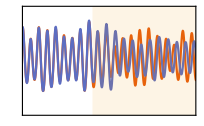

```mathematica
Magnify[fig[1], 1]
```

```mathematica
fig[2] = ListPlot[{data[[1]][[All, {1, 165}]], data[[2]][[All, {1, 165}]]},
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
PlotLabel->MaTeX@"x^2_4",
FrameLabel->{MaTeX@"t", None},
FrameTicks->{{With[{ticks=-0.2+0.2Range[0,6]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=30Range[0,12]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
PlotRange->{{80, 170}, Automatic},
ImageSize->7.2cm,
Joined->True,
PlotRangePadding->{1.0, 0.1},
Epilog->{colors[[3]],Opacity[0.1],Rectangle[{100,-0.4},{175,0.4}]},
ImageMargins->0
];
```

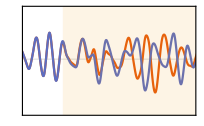

```mathematica
Magnify[fig[2], 1]
```

```mathematica
plt1 = Legended[Grid[{{fig[1], "", fig[2]}, {"", "", ""}}], Placed[LineLegend[{colors[[1]], colors[[2]]},MaTeX/@{"\\text{original}", "\\text{perturbed}"}, LegendLayout->"Row"], {Bottom, Bottom}]]
```

-Graphics- |  | -Graphics-
 |  |

```mathematica
Export[plotsDir<>"/2-chaos.pdf", plt1]
```

../../../plots/plots-thesis/2-chaos.pdf

```mathematica
n = Length[data];
z = Monitor[Table[Mean@data[[All,kkk, aaa+1]], {kkk, 1, Length[data[[1]]]},{aaa, 1, $K(($N)^2-1)}], ProgressIndicator[(kkk-1)/(Length[data[[1]]]-1)]];
```

```mathematica
size = Monitor[Table[1/n Sum[1/2 Total[#^2&/@(z[[k]] - data[[A, k, 2;;$K(($N)^2-1)+1]])], {A, 1, n}], {k, 1, Length[z]}], ProgressIndicator[(k-1)/(Length[z]-1)]];
```

```mathematica
m = Mean@Log[10, size[[2000;;]]]
```

0.398584

```mathematica
t = data[[1, All, 1]];
```

```mathematica
{t1, m1} = SelectFirst[Thread[{t, Log[10, size]}], Abs[#[[2]]-m]<=0.06&]
```

{143.7,0.348477}

```mathematica
fig[3]= ListLogPlot[Thread[{data[[1, All, 1]], size}],
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
GridLines->{{t1}, None},
GridLinesStyle->Directive[colors[[2]], Thickness[0.005],Opacity[1], Dashed],
FrameLabel->MaTeX/@{"t", "R^2"},
FrameTicks->{{With[{ticks=Range[-11, 2, 3]},Thread[{10^ticks,MaTeX[Table[Superscript[10, l], {l, ticks}],"DisplayStyle"->False]}]],None},{With[{ticks=100Range[0,5]//Chop},Thread[{Join[ticks, {t1}],MaTeX[Join[ticks, {"t_S"}],"DisplayStyle"->False]}]],None}},
PlotRange->{{0, 400}, Automatic},
Epilog->{colors[[3]],Opacity[0.1],Rectangle[{t1,-300},{400,100}],
Text[
MaTeX["\\text{linear growth}","DisplayStyle"->False],
Scaled[{0.17,0.12}]
],
Text[
MaTeX["\\text{saturation}","DisplayStyle"->False],
Scaled[{0.67,0.12}]
]
},
Joined->True,
ImageSize->14cm
];
```

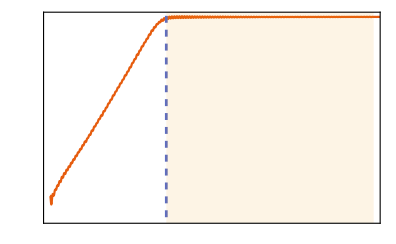

```mathematica
Magnify[fig[3], 1]
```

```mathematica
Export[plotsDir<>"/2-saturation.pdf", fig[3]]
```

../../../plots/plots-thesis/2-saturation.pdf